```mathematica
On[Assert]
ClearAll["`*"]
```

```mathematica
ez={0,0,1};
k={kx,ky,kz};
kϵzz={kx/Sqrt[ϵzz],ky/Sqrt[ϵzz],kz};
ϵ=DiagonalMatrix[{1,1,ϵzz}];
W=k⊗k-(k.k) IdentityMatrix[3]+k0^2 ϵ;
g[k_]:=1/(k.k-k0^2);
h[k_]:=1/(k[[1]]^2+k[[2]]^2)g[k];
inverseW=1/ϵzz/k0^2(k⊗k-k0^2ez⊗ez)g[kϵzz]-1/ϵzz(k-kz ez)⊗(k-kz ez)h[kϵzz]-(k×ez)⊗(k×ez)h[k];
Assert[Simplify[inverseW.W]==IdentityMatrix[3]]
Gk=inverseW//Simplify;
```

```mathematica
expr=Det@W/.{k0->2π,ϵzz->3};
lim=12;
ContourPlot3D[{expr==0,kx^2+ky^2+3 kz^2==3(2π)^2,kz^2==(2π)^2},{kx,0,lim},{ky,-0,lim},{kz,0,lim}]
```

-Graphics3D-

```mathematica
G∞=-1/(k0^2-kz^2) /(k0^2-kx^2-ky^2-kz^2)((k0^2-kz^2)DiagonalMatrix[{1,1,0}]-{kx,ky,0}⊗{kx,ky,0});
expr=-Limit[Inverse@W,ϵzz->∞]//Simplify;
Assert[Max@Abs@Simplify[G∞-expr]==0]
```

```mathematica
maxOrder=6;
Table[NIntegrate[Conjugate@SphericalHarmonicY[l,0,θ,0]Cos[θ]^2Sin[θ],{θ,0,π}],{l,0,maxOrder}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.0000120929}. NIntegrate obtained -1.23599×10^-17 and 1.11365×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.68749}. NIntegrate obtained -1.02457×10^-17 and 1.92719×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.1415805607065542416335380757064221768359857378527522087097167969}. NIntegrate obtained -2.5533×10^-17 and 1.9094×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.188063,-1.23599×10^-17,0.168209,-1.02457×10^-17,-2.5533×10^-17,-1.60462×10^-17,-1.64799×10^-17}

```mathematica
Table[Simplify@TransformedField["Spherical"->"Cartesian",r^l SphericalHarmonicY[l,0,θ,ϕ],{r,θ,ϕ}->{x,y,z}],{l,3,5}]
```

{1/4 √(7/π) z (-3 x^2-3 y^2+2 z^2),(3 (3 x^4+3 y^4-24 y^2 z^2+8 z^4+6 x^2 (y^2-4 z^2)))/(16 √π),1/16 √(11/π) z (15 x^4+15 y^4-40 y^2 z^2+8 z^4+10 x^2 (3 y^2-4 z^2))}

```mathematica
Simplify@TransformedField["Cylindrical"->"Cartesian",
Limit[Simplify@TransformedField["Cartesian"->"Cylindrical",Gk,{kx,ky,kz}->{kρ,kϕ,kzc}],ϵzz->∞],
{kρ,kϕ,kzc}->{kx,ky,kz}]//MatrixForm
```

((-k0^2+kx^2+kz^2)/((k0^2-kz^2) (-k0^2+kx^2+ky^2+kz^2)) | (kx ky)/((k0^2-kz^2) (-k0^2+kx^2+ky^2+kz^2)) | 0
(kx ky)/((k0^2-kz^2) (-k0^2+kx^2+ky^2+kz^2)) | (-k0^2+ky^2+kz^2)/((k0^2-kz^2) (-k0^2+kx^2+ky^2+kz^2)) | 0
0 | 0 | 0)

```mathematica
$Assumptions=$Assumptions&&z∈Reals;
h0cyl=(-ⅇ^(ⅈ k0 z) ExpIntegralEi[ⅈ k0 (-z+√(z^2+ρ^2))]-ⅇ^(-ⅈ k0 z) ExpIntegralEi[ⅈ k0 (z+√(z^2+ρ^2))](*+ⅇ^(ⅈ k0 Abs[z]) Log[ρ^2]*))/(8k0 π ⅈ);
Limit[ρ D[h0cyl,ρ],ρ->0]
```

(ⅈ ⅇ^(ⅈ k0 Abs[z]))/(4 k0 π)

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
h0=(-ⅇ^(ⅈ k0 z) ExpIntegralEi[ⅈ k0 (-z+√(z^2+ρ^2))]-ⅇ^(-ⅈ k0 z) ExpIntegralEi[ⅈ k0 (z+√(z^2+ρ^2))](*+ⅇ^(ⅈ k0 Abs[z]) Log[ρ^2]*))/(8k0 π ⅈ)/.ρ->Sqrt[x^2+y^2];
derivativeSubs={ Abs'[z_]:>Sign[z], Abs''[z_]:>2DiracDelta[z]};
k0^2h0+Laplacian[h0,{x,y,z}]/.derivativeSubs//Simplify//Expand
k0^2h0+Laplacian[h0,{z}]/.derivativeSubs//Simplify//Expand
GChenLar={{(-k0^2h0-D[h0,x,x]-D[h0,z,z])//Simplify,0,0},{-D[h0,x,y]//Simplify,0,0},{0,0,0}};
k0^2GChenLar+Laplacian[GChenLar,{x,y,z}]//Simplify//Expand
```

0

(ⅇ^(ⅈ k0 √(x^2+y^2+z^2)))/(4 π √(x^2+y^2+z^2))

{{0,0,0},{0,0,0},{0,0,0}}

(ⅇ^(-2 π Im[√(x^2+z^2)]))/(8 π^2 Abs[x]^2)

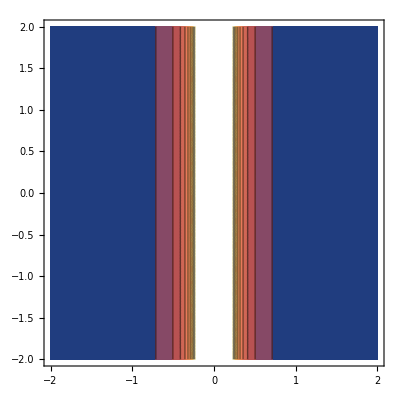

```mathematica
expr=Abs@GChenLar[[1,1]]/.{y->0,k0->2π}
ContourPlot[expr,{x,-2,2},{z,-2,2}]
```

```mathematica
f=DiracDelta[x,y]Sin[k0 z]Sign[z]/2/k0;
k0^2f+D[f,z,z]/.{Sign'[x_]:>2DiracDelta[x],Sign''[x_]:>2DiracDelta'[x]}//Simplify;
Assert[Simplify[2 DiracDelta[x] DiracDelta[y] DiracDelta[z]+(DiracDelta[x] DiracDelta[y] (-1)k0 DiracDelta[z])/k0]==DiracDelta[x] DiracDelta[y] DiracDelta[z]]
```

Log[1.21 Sin[θ]^2] Sign[Cos[θ]] Sin[13.823 Cos[θ]]

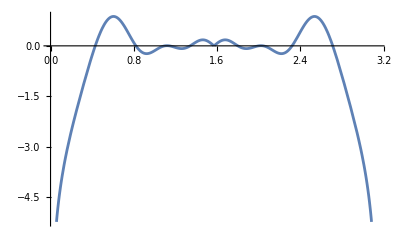

```mathematica
f2=Log[x^2+y^2]Sin[2π z]Sign[z];
plotExpr=Simplify@TransformedField["Cartesian"->"Spherical",Log[1(x^2+y^2)]Sin[2 2π z]Sign[z],{x,y,z}->{r,θ,ϕ}]/.r->1.1
Plot[plotExpr,{θ,0,π},PlotRange->Automatic]
```

```mathematica
f=(DiracDelta[x] DiracDelta[y] Sign[z] Sin[k0 z])/k0;
(k0^2f+Laplacian[f,{x,z}])/.{Sign'->2DiracDelta,Sign''->2DiracDelta'}//Simplify
```

2 Cos[k0 z] DiracDelta[x] DiracDelta[y] (2 DiracDelta)[z]+(DiracDelta[x] DiracDelta[y] Sin[k0 z] (2 DiracDelta')[z])/k0+(DiracDelta[y] Sign[z] Sin[k0 z] DiracDelta''[x])/k0

```mathematica
(-1(kx^2+ky^2))/((k0^2-kz^2) (-k0^2+kx^2+ky^2+kz^2))//Apart
```

1/(2 k0 (-k0+kz))-1/(2 k0 (k0+kz))-1/(-k0^2+kx^2+ky^2+kz^2)

```mathematica
(-k0^4+kx^2)/(k0^2 (-k0^2+kx^2+ky^2+kz^2))//Apart
```

-((k0^2-kx) (k0^2+kx))/(k0^2 (-k0^2+kx^2+ky^2+kz^2))

```mathematica
g0=Exp[ⅉ k0 Sqrt[x^2+y^2+z^2]]/(4π  Sqrt[x^2+y^2+z^2]);
h0=-(ⅈ ⅇ^(ⅈ k0 z) ExpIntegralEi[ⅈ k0 (-z+√(x^2+y^2+z^2))])/(8 k0 π)-(ⅈ ⅇ^(-ⅈ k0 z) ExpIntegralEi[ⅈ k0 (z+√(x^2+y^2+z^2))])/(8 k0 π)-(ⅈ ⅇ^(-ⅈ k0 Abs@ z) Log[x^2+y^2])/(8 k0 π);
GChenLar={{(-k0^2h0-D[h0,x,x]-D[h0,z,z])//Simplify,0,0},{-D[h0,x,y]//Simplify,0,0},{0,0,0}};
```

```mathematica
Laplacian[h0,{x,y,z}]+k0^2 h0//Simplify
```

(ⅈ ⅇ^(-ⅈ k0 Abs[z]) Log[x^2+y^2] (-k0+k0 Abs'[z]^2+ⅈ Abs''[z]))/(8 π)

```mathematica
Apart[1/((k0^2-kz^2) (-k0^2+kx^2+ky^2+kz^2))]
```

-1/(2 k0 (kx^2+ky^2) (-k0+kz))+1/(2 k0 (kx^2+ky^2) (k0+kz))+1/((kx^2+ky^2) (-k0^2+kx^2+ky^2+kz^2))

```mathematica
DSolve[k0^2 f[z]+D[f[z],z,z]==DiracDelta[x,y,z],f,z]
```

{{f→Function[{z},C[1] Cos[k0 z]+C[2] Sin[k0 z]+(DiracDelta[x] DiracDelta[y] HeavisideTheta[z] Sin[k0 z])/k0]}}

```mathematica
k0^2h0+D[h0,z,z]//Simplify
```

-(ⅇ^(ⅈ k0 √(x^2+y^2+z^2)))/(4 π √(x^2+y^2+z^2))

```mathematica
Integrate[Exp[ⅉ k0 (Sqrt[1+x^2]+x)]/Sqrt[1+x^2],x]
```

∫(ⅇ^(ⅈ k0 (x+√(1+x^2))))/(√(1+x^2))ⅆx

```mathematica
inverseW//Simplify//Grid
Limit[inverseW,ϵzz->1]//Simplify//Grid
Limit[inverseW,ϵzz->∞]//Simplify//Grid
```

(kx^2 (kx^2+ky^2+kz^2)+k0^4 ϵzz-k0^2 (ky^2+kz^2 ϵzz+kx^2 (1+ϵzz)))/(k0^2 (-k0^2+kx^2+ky^2+kz^2) (kx^2+ky^2+(-k0^2+kz^2) ϵzz)) | (kx ky (kx^2+ky^2+kz^2-k0^2 ϵzz))/(k0^2 (-k0^2+kx^2+ky^2+kz^2) (kx^2+ky^2+(-k0^2+kz^2) ϵzz)) | (kx kz)/(k0^2 (kx^2+ky^2+(-k0^2+kz^2) ϵzz))
(kx ky (kx^2+ky^2+kz^2-k0^2 ϵzz))/(k0^2 (-k0^2+kx^2+ky^2+kz^2) (kx^2+ky^2+(-k0^2+kz^2) ϵzz)) | (ky^2 (kx^2+ky^2+kz^2)+k0^4 ϵzz-k0^2 (kx^2+kz^2 ϵzz+ky^2 (1+ϵzz)))/(k0^2 (-k0^2+kx^2+ky^2+kz^2) (kx^2+ky^2+(-k0^2+kz^2) ϵzz)) | (ky kz)/(k0^2 (kx^2+ky^2+(-k0^2+kz^2) ϵzz))
(kx kz)/(k0^2 (kx^2+ky^2+(-k0^2+kz^2) ϵzz)) | (ky kz)/(k0^2 (kx^2+ky^2+(-k0^2+kz^2) ϵzz)) | -(k0^2-kz^2)/(k0^2 (kx^2+ky^2+(-k0^2+kz^2) ϵzz))

-(k0^2-kx^2)/(k0^2 (-k0^2+kx^2+ky^2+kz^2)) | (kx ky)/(k0^2 (-k0^2+kx^2+ky^2+kz^2)) | (kx kz)/(k0^2 (-k0^2+kx^2+ky^2+kz^2))
(kx ky)/(k0^2 (-k0^2+kx^2+ky^2+kz^2)) | -(k0^2-ky^2)/(k0^2 (-k0^2+kx^2+ky^2+kz^2)) | (ky kz)/(k0^2 (-k0^2+kx^2+ky^2+kz^2))
(kx kz)/(k0^2 (-k0^2+kx^2+ky^2+kz^2)) | (ky kz)/(k0^2 (-k0^2+kx^2+ky^2+kz^2)) | (-k0^2+kz^2)/(k0^2 (-k0^2+kx^2+ky^2+kz^2))

-(k0^2-kx^2-kz^2)/((k0^2-kz^2) (-k0^2+kx^2+ky^2+kz^2)) | (kx ky)/((k0^2-kz^2) (-k0^2+kx^2+ky^2+kz^2)) | 0
(kx ky)/((k0^2-kz^2) (-k0^2+kx^2+ky^2+kz^2)) | -(k0^2-ky^2-kz^2)/((k0^2-kz^2) (-k0^2+kx^2+ky^2+kz^2)) | 0
0 | 0 | 0

```mathematica
Simplify@Inverse@Limit[k⊗k-(k.k) IdentityMatrix[3]+k0^2 DiagonalMatrix[{ϵzz,ϵzz,1}],ϵzz->0]//Grid
```

(kx^2/k0^2-(kx^2+kz^2)/(kx^2+ky^2+kz^2))/kz^2 | (kx ky (-k0^2+kx^2+ky^2+kz^2))/(k0^2 kz^2 (kx^2+ky^2+kz^2)) | kx/(k0^2 kz)
(kx ky (-k0^2+kx^2+ky^2+kz^2))/(k0^2 kz^2 (kx^2+ky^2+kz^2)) | (ky^2/k0^2-(ky^2+kz^2)/(kx^2+ky^2+kz^2))/kz^2 | ky/(k0^2 kz)
kx/(k0^2 kz) | ky/(k0^2 kz) | 1/k0^2

```mathematica
Curl[Curl[{Ex@@R,Ey@@R,0},R],R]//MatrixForm
```

(-Ex^(0,0,2)[x,y,z]-Ex^(0,2,0)[x,y,z]+Ey^(1,1,0)[x,y,z]
-Ey^(0,0,2)[x,y,z]+Ex^(1,1,0)[x,y,z]-Ey^(2,0,0)[x,y,z]
Ey^(0,1,1)[x,y,z]+Ex^(1,0,1)[x,y,z])

```mathematica
re=Sqrt[ϵzz]ρ;
c={0,0,1};
iTransverse=DiagonalMatrix[{1,1,0}];
ϵinvϵ=ϵzz iTransverse;
expTerm=Exp[ⅉ k0 re]/re;
Glar=(ϵinvϵ-(ϵinvϵ.R)⊗(ϵinvϵ.R)/re^2)expTerm-
ϵzz expTerm(R×c)⊗(R×c)/ρ^2-
ϵzz Exp[ⅉ k0 re/2]/re Sin[k0 re/2]/(k0 re/2)(
IdentityMatrix[3]-c⊗c-2(R×c)⊗(R×c)/ρ^2
);
Glar=1/(4π)Glar;
4π k0 ρ/expTerm Glar/Sqrt[ϵzz]/.{x->ρ Cos[ϕ],y->ρ Sin[ϕ]}//Simplify//Grid
```

ⅈ-ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)+k0 √ϵzz ρ-((2 ⅈ-2 ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)+k0 √ϵzz ρ) R×{0,0,1}⊗R×{0,0,1})/ρ^2-(k0 ({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)⊗({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R))/(ϵzz^(3/2) ρ) | 1/ρ^2((-2 ⅈ+2 ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)-k0 √ϵzz ρ) R×{0,0,1}⊗R×{0,0,1}-1/ϵzz^(3/2)k0 ρ ({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)⊗({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)) | 1/ρ^2((-2 ⅈ+2 ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)-k0 √ϵzz ρ) R×{0,0,1}⊗R×{0,0,1}-1/ϵzz^(3/2)k0 ρ ({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)⊗({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R))
1/ρ^2((-2 ⅈ+2 ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)-k0 √ϵzz ρ) R×{0,0,1}⊗R×{0,0,1}-1/ϵzz^(3/2)k0 ρ ({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)⊗({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)) | ⅈ-ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)+k0 √ϵzz ρ-((2 ⅈ-2 ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)+k0 √ϵzz ρ) R×{0,0,1}⊗R×{0,0,1})/ρ^2-(k0 ({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)⊗({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R))/(ϵzz^(3/2) ρ) | 1/ρ^2((-2 ⅈ+2 ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)-k0 √ϵzz ρ) R×{0,0,1}⊗R×{0,0,1}-1/ϵzz^(3/2)k0 ρ ({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)⊗({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R))
1/ρ^2((-2 ⅈ+2 ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)-k0 √ϵzz ρ) R×{0,0,1}⊗R×{0,0,1}-1/ϵzz^(3/2)k0 ρ ({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)⊗({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)) | 1/ρ^2((-2 ⅈ+2 ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)-k0 √ϵzz ρ) R×{0,0,1}⊗R×{0,0,1}-1/ϵzz^(3/2)k0 ρ ({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)⊗({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)) | 1/ρ^2((-2 ⅈ+2 ⅈ ⅇ^(-ⅈ k0 √ϵzz ρ)-k0 √ϵzz ρ) R×{0,0,1}⊗R×{0,0,1}-1/ϵzz^(3/2)k0 ρ ({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R)⊗({{ϵzz,0,0},{0,ϵzz,0},{0,0,0}}.R))

```mathematica
R={x,y,z};
u={0,0,1};
RcrossU=R×u;
RcrossU2=RcrossU.RcrossU;
ϵ=DiagonalMatrix[{1,1,ϵzz}];
ϵu=ϵ0 ϵzz;
ϵuni=ϵ0 ϵ;
rϵ=ϵu R.Inverse[ϵuni].R//Simplify;
gϵuni=ⅇ^(ⅈ k0 Sqrt[rϵ])/(4π Sqrt[rϵ])//Simplify;
rμ=R.R//Simplify;
gμuni=ⅇ^(ⅈ k0 Sqrt[rμ])/(4π Sqrt[rμ])//Simplify;
DelDel[f_]:=Table[D[f,R[[i]],R[[j]]],{i,1,3},{j,1,3}];
B=RcrossU⊗RcrossU/RcrossU2(ϵu/ϵ0 gϵuni-gμuni)+1/(ⅈ k0 RcrossU2)(IdentityMatrix[3]-u⊗u-2RcrossU⊗RcrossU/RcrossU2)(gϵuni Sqrt[rϵ]-gμuni Sqrt[rμ]);
(*GChen=Simplify[Simplify[Simplify[-B+ϵu Inverse[ϵuni]gϵuni+1/(k0^2)DelDel[gϵuni]/.{
x->ρ Cos[ϕ],
y->ρ Sin[ϕ],
z^2+(x^2+y^2) ϵzz->ρ^2 ϵzz
}]/.{1-ⅈ k0 √(ϵzz ρ^2)->-ⅈ k0 √ϵzz ρ,
3-ⅈ k0 √(ϵzz ρ^2)->-ⅈ k0 √ϵzz ρ,
-ⅈ k0+3/(√(ϵzz ρ^2))->-ⅈ k0,
3-k0^2 ϵzz ρ^2-3 ⅈ k0 √(ϵzz ρ^2)->-k0^2 ϵzz ρ^2,
√(ϵzz ρ^2)->ρ √ϵzz
},Assumptions->ρ∈Reals&&ϵzz∈Reals&&ρ>0],
{z^2+ρ^2->r^2}
]*)
```

```mathematica
GChenLar={{(ⅇ^(ⅈ k0 r) k0 ρ^2-ⅈ ⅇ^(ⅈ k0 √ϵzz ρ) r-(ⅈ ⅇ^(ⅈ k0 √ϵzz ρ) r+ⅇ^(ⅈ k0 r) (k0 ρ^2+2 ⅈ r)) Cos[2 ϕ])/(8 k0 π ρ^2 r),((-ⅈ ⅇ^(ⅈ k0 √ϵzz ρ) k0+ⅇ^(ⅈ k0 r) k0 (-2 ⅈ-(k0 ρ^2)/r)) Sin[2 ϕ])/(8 k0^2 π ρ^2),0},{((-ⅈ ⅇ^(ⅈ k0 √ϵzz ρ) k0+ⅇ^(ⅈ k0 r) k0 (-2 ⅈ-(k0 ρ^2)/r)) Sin[2 ϕ])/(8 k0^2 π ρ^2),(k0 ρ (ⅇ^(ⅈ k0 r) k0 ρ^2-ⅈ ⅇ^(ⅈ k0 √ϵzz ρ) r)+(ⅈ ⅇ^(ⅈ k0 √ϵzz ρ) k0  ρ r+ⅇ^(ⅈ k0 r) k0 ρ (k0 ρ^2+2 ⅈ r)) Cos[2 ϕ])/(8 k0^2 π ρ^3 r),0},{0,0,0}};
```

-ⅈ ⅇ^(ⅈ k0 √ϵzz ρ) r+ⅇ^(ⅈ k0 r) k0 ρ^2-(ⅈ ⅇ^(ⅈ k0 √ϵzz ρ) r+ⅇ^(ⅈ k0 r) (2 ⅈ r+k0 ρ^2)) Cos[2 ϕ]

-ⅈ ⅇ^(ⅈ k0 √ϵzz ρ) r+ⅇ^(ⅈ k0 r) k0 ρ^2+(ⅈ ⅇ^(ⅈ k0 √ϵzz ρ) r+ⅇ^(ⅈ k0 r) (2 ⅈ r+k0 ρ^2)) Cos[2 ϕ]

```mathematica
GChen=Simplify@TransformedField["Cartesian"->"Cylindrical",(-B+ϵu Inverse[ϵuni]gϵuni+1/(k0^2)DelDel[gϵuni]),R->{ρ,ϕ,zp}]
```

{{(-ⅈ ⅇ^(ⅈ k0 √(zp^2+ρ^2)) k0+(ⅇ^(ⅈ k0 √(zp^2+ϵzz ρ^2)) (k0 zp^4 (k0 ϵzz ρ^2+ⅈ √(zp^2+ϵzz ρ^2))+ϵzz^2 ρ^4 (2-ⅈ k0 √(zp^2+ϵzz ρ^2))+zp^2 ϵzz ρ^2 (-1+k0^2 ϵzz ρ^2+3 ⅈ k0 √(zp^2+ϵzz ρ^2))))/((zp^2+ϵzz ρ^2)^(5/2)))/(4 k0^2 π ρ^2),0,-(ⅇ^(ⅈ k0 √(zp^2+ϵzz ρ^2)) zp ϵzz ρ (-3+3 ⅈ k0 √(zp^2+ϵzz ρ^2)+k0^2 (zp^2+ϵzz ρ^2)))/(4 k0^2 π (zp^2+ϵzz ρ^2)^(5/2))},{0,(ⅇ^(ⅈ k0 √(zp^2+ρ^2)) k0 (ⅈ+(k0 ρ^2)/(√(zp^2+ρ^2)))+ⅇ^(ⅈ k0 √(zp^2+ϵzz ρ^2)) (-(ϵzz ρ^2)/((zp^2+ϵzz ρ^2)^(3/2))-(ⅈ k0 zp^2)/(zp^2+ϵzz ρ^2)))/(4 k0^2 π ρ^2),0},{-(ⅇ^(ⅈ k0 √(zp^2+ϵzz ρ^2)) zp ϵzz ρ (-3+3 ⅈ k0 √(zp^2+ϵzz ρ^2)+k0^2 (zp^2+ϵzz ρ^2)))/(4 k0^2 π (zp^2+ϵzz ρ^2)^(5/2)),0,(ⅇ^(ⅈ k0 √(zp^2+ϵzz ρ^2)) (ϵzz ρ^2 (-1+k0^2 ϵzz ρ^2+ⅈ k0 √(zp^2+ϵzz ρ^2))+zp^2 (2+k0^2 ϵzz ρ^2-2 ⅈ k0 √(zp^2+ϵzz ρ^2))))/(4 k0^2 π (zp^2+ϵzz ρ^2)^(5/2))}}

```mathematica
$Assumptions=$Assumptions&&ϵzz∈Reals&&ϵzz>0&&ρ∈Reals&&ρ>0&&r∈Reals&&r>0;
Simplify[{{(-ⅈ ⅇ^(ⅈ k0 √(zp^2+ρ^2)) k0+(ⅇ^(ⅈ k0 √(ϵzz ρ^2)) ( ρ^4 (-ⅈ k0 √(ρ^2))))/((ρ^2)^(5/2)))/(4 k0^2 π ρ^2),0,-(ⅇ^(ⅈ k0 √(ϵzz ρ^2)) zp ϵzz ρ (k0^2 (ϵzz ρ^2)))/(4 k0^2 π (ϵzz ρ^2)^(5/2))},{0,(ⅇ^(ⅈ k0 √(zp^2+ρ^2)) k0 (ⅈ+(k0 ρ^2)/(√(zp^2+ρ^2)))+ⅇ^(ⅈ k0 √(ϵzz ρ^2)) (-(ϵzz ρ^2)/((ϵzz ρ^2)^(3/2))))/(4 k0^2 π ρ^2),0},{-(ⅇ^(ⅈ k0 √(ϵzz ρ^2)) zp ϵzz ρ (k0^2 (ϵzz ρ^2)))/(4 k0^2 π (ϵzz ρ^2)^(5/2)),0,(ⅇ^(ⅈ k0 √(ϵzz ρ^2)) (ϵzz ρ^2 (k0^2 ϵzz ρ^2)+zp^2 (k0^2 ϵzz ρ^2)))/(4 k0^2 π (ϵzz ρ^2)^(5/2))}}]
```

{{-(ⅈ (ⅇ^(ⅈ k0 √ϵzz ρ)+ⅇ^(ⅈ k0 √(zp^2+ρ^2))))/(4 k0 π ρ^2),0,-(ⅇ^(ⅈ k0 √ϵzz ρ) zp)/(4 π √ϵzz ρ^2)},{0,(-ⅇ^(ⅈ k0 √ϵzz ρ)/(√ϵzz ρ)+ⅇ^(ⅈ k0 √(zp^2+ρ^2)) k0 (ⅈ+(k0 ρ^2)/(√(zp^2+ρ^2))))/(4 k0^2 π ρ^2),0},{-(ⅇ^(ⅈ k0 √ϵzz ρ) zp)/(4 π √ϵzz ρ^2),0,(ⅇ^(ⅈ k0 √ϵzz ρ) (zp^2+ϵzz ρ^2))/(4 π ϵzz^(3/2) ρ^3)}}

```mathematica
Simplify@TransformedField["Cylindrical"->"Cartesian",Simplify@{{-(ⅈ (ⅇ^(ⅈ k0 √ϵzz ρ)+ⅇ^(ⅈ k0 √(zp^2+ρ^2))))/(4 k0 π ρ^2),0,0},{0,(ⅇ^(ⅈ k0 √(zp^2+ρ^2)) k0 (ⅈ+(k0 ρ^2)/(√(zp^2+ρ^2))))/(4 k0^2 π ρ^2),0},{0,0,0}},{ρ,ϕ,zp}->R]
```

{{(-ⅈ ⅇ^(ⅈ k0 √((x^2+y^2) ϵzz)) x^2 √(x^2+y^2+z^2)+ⅇ^(ⅈ k0 √(x^2+y^2+z^2)) (k0 y^2 (x^2+y^2)-ⅈ (x^2-y^2) √(x^2+y^2+z^2)))/(4 k0 π (x^2+y^2)^2 √(x^2+y^2+z^2)),-(x y (ⅈ ⅇ^(ⅈ k0 √((x^2+y^2) ϵzz)) √(x^2+y^2+z^2)+ⅇ^(ⅈ k0 √(x^2+y^2+z^2)) (k0 (x^2+y^2)+2 ⅈ √(x^2+y^2+z^2))))/(4 k0 π (x^2+y^2)^2 √(x^2+y^2+z^2)),0},{-(x y (ⅈ ⅇ^(ⅈ k0 √((x^2+y^2) ϵzz)) √(x^2+y^2+z^2)+ⅇ^(ⅈ k0 √(x^2+y^2+z^2)) (k0 (x^2+y^2)+2 ⅈ √(x^2+y^2+z^2))))/(4 k0 π (x^2+y^2)^2 √(x^2+y^2+z^2)),(-ⅈ ⅇ^(ⅈ k0 √((x^2+y^2) ϵzz)) y^2 √(x^2+y^2+z^2)+ⅇ^(ⅈ k0 √(x^2+y^2+z^2)) (k0 x^2 (x^2+y^2)+ⅈ (x^2-y^2) √(x^2+y^2+z^2)))/(4 k0 π (x^2+y^2)^2 √(x^2+y^2+z^2)),0},{0,0,0}}

```mathematica
Curl[Curl[{Ex@@R,Ey@@R,Ez@@R},R],R][[1]]
```

-Ex^(0,0,2)[x,y,z]-Ex^(0,2,0)[x,y,z]+Ez^(1,0,1)[x,y,z]+Ey^(1,1,0)[x,y,z]

```mathematica
nabla={dx,dy,dz};
(nabla⊗nabla-(nabla.nabla) IdentityMatrix[3]+k0^2 ϵ).{Ex@@R,Ey@@R,Ez@@R}//MatrixForm
```

((-dy^2-dz^2+k0^2) Ex[x,y,z]+dx dy Ey[x,y,z]+dx dz Ez[x,y,z]
dx dy Ex[x,y,z]+(-dx^2-dz^2+k0^2) Ey[x,y,z]+dy dz Ez[x,y,z]
dx dz Ex[x,y,z]+dy dz Ey[x,y,z]+(-dx^2-dy^2+k0^2 ϵzz) Ez[x,y,z])

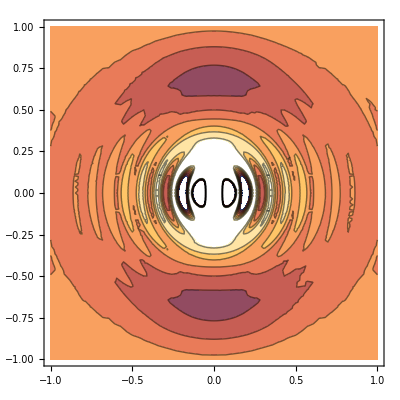

```mathematica
ContourPlot[Im@GChen[[1,1]]/.{k0->2π,ϵzz->100,z->.0001},{x,-1,1},{y,-1,1},PlotRange->Automatic]
```